```mathematica
Ground to Rydberg Rabi Frequency
```

M. Kwon

```mathematica
(*Physical Constants *)
ℏ=1.054571628*10^(-34); (* m^2 kg/s*)
e=1.602176487*10^(-19); (* C*)
ϵ0=8.854187817*10^-12;(*F/m*)
μ0=4*π*10^-7;(*H/m, Permeability*)
me=9.10938215*10^(-31); (*kg*)
c=299792458;(*Speed of Light in SI Unit*)
kB=1.3806504*10^-23; (*Boltzman's Constant in SI unit *)
a0=0.0529*10^-9 ;(*Bohr Radius. meter*)
EH=27.2*1.6*10^-19; (*Hartree Energy*)
μB=9.27400915*10^-24;(*Bohr Magneton*)
mp=1.6726219×10^-27;  (* Proton mass *)
```

```mathematica
Quantum Defect Theory (Rb 87)
```

```mathematica
δ0[l_,j_]:=Which[l==0&&j==1/2,3.1311807,l==2&&j==3/2,1.3480948,l==2&&j==5/2,1.3464622,l==1&&j==3/2,2.6416737];
δ2[l_,j_]:=Which[l==0&&j==1/2,0.1787,l==2&&j==3/2,-0.6054,l==2&&j==5/2,-0.5940,l==1&&j==3/2,0.2950];
δ[n_,l_,j_]:=δ0[l,j]+δ2[l,j]/(n-δ0[l,j])^2;
```

```mathematica
Rydberg Energy levels and Zeeman terms
```

```mathematica
Energy[n_,l_,j_]:=-EH/(2(n-δ[n,l,j])^2)/.EH->6579.683920711 (* in THz*)
gJ[L_,S_,J_]:=3/2-(L(L+1)-S(S+1))/(2J(J+1));

r2Exp[n_,l_,aμ_]:=1/2 aμ^2 n^2 (1-3 l-3 l^2+5 n^2); (* <r^2>. Subscript[a, μ] is reduced Bohr radius *)
sinsquareY00[l1_,l2_,m1_,m2_]:=2/3*KroneckerDelta[m1,m2]KroneckerDelta[l1,l2];
sinsquareY20[l1_,l2_,m1_,m2_]:=-KroneckerDelta[m1,m2](4√π)/(3√5)(KroneckerDelta[l1,l2]Sqrt[5/(4π)]ClebschGordan[{l1,0},{l1,0},{2,0}]ClebschGordan[{l1,m1},{l1,m1},{2,0}]
+KroneckerDelta[l1+2,l2]Sqrt[5(2l1+1)/(4π(2l1+5))]ClebschGordan[{l1+2,0},{l1,0},{2,0}]ClebschGordan[{l1+2,m1},{l1,m1},{2,0}]
+KroneckerDelta[l1-2,l2]Sqrt[5(2l1+1)/(4π(2l1-3))]ClebschGordan[{l1-2,0},{l1,0},{2,0}]ClebschGordan[{l1-2,m1},{l1,m1},{2,0}]);
sinsquare[l1_,l2_,m1_,m2_]:=sinsquareY00[l1,l2,m1,m2]+sinsquareY20[l1,l2,m1,m2];
HZeeman[B_,g_,mJ_]:=μB g mJ B; (* B in Tesla! *)
Hdimagnetic[B_,n_,l_,m_,aμ_]:=(2/EH)(μB B)^2/8*(1/a0)^2 r2Exp[n,l,aμ]sinsquare[l,l,m,m];
JtoMHz=10^-6/(2π ℏ); (* To convert the energy to Mhz *)
```

```mathematica
Radial Matrix elements WKB approx
```

```mathematica
factors[γ2_,l2_,γ1_,l1_]:=((1-y)/π Sin[π(γ2-γ1)]+1/2 AngerJ[-1+γ1-γ2,y (-γ1+γ2)]-1/2 AngerJ[1+γ1-γ2,y (-γ1+γ2)]+Sqrt[y^-2-1](AngerJ[γ1-γ2,y (-γ1+γ2)]-Sin[π (γ2-γ1)]/(π(γ2-γ1))));
Rwkb[γ2_,n2_,l2_,γ1_,n1_,l1_]:=(-1)^(n2-n1)γc^5/((γ1 γ2)^(3/2)(γ2-γ1)) factors[γ2,l2,γ1,l1]//.{y->(1-((l1+l2+1)/(2γc))^2)^(1/2),γc->(2 (γ1 γ2)^2/(γ1+γ2))^(1/3)};Rwkb[5-δ[5,1,3/2],5,1,5-δ[5,0,1/2],5,0] ;(* Radial Matrix Element for 5p3/2 and 5s1/2*)
Rwkb[n2-δ[n2,2,5/2],n2,2,n1-δ[n1,1,3/2],n1,0]/.{n1->5,n2->97};(* Radial Matrix Element for 5p3/2 and 97d5/2*)
ToReduced[L2_,J2_,L1_,J1_]:=(-1)^(1+1/2+L2+J1)Sqrt[(2J1+1)(2J2+1)]SixJSymbol[{L1,1/2,J1},{J2,1,L2}](-1)^(L2+(1+L1+L2)/2)Sqrt[Max[L1,L2]]
ToReduced[2,5/2,1,3/2] Rwkb[n2-δ[n2,2,5/2],n2,2,n1-δ[n1,1,3/2],n1,0]/.{n1->5,n2->97,L1->1,L2->2}
```

-0.0106006

```mathematica
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
Off[SixJSymbol::tri];


Efield[intensity_]:=Sqrt[2 intensity /(c ϵ0)];
Δhfs[A_,f_,nucI_,jp_]:=2π A/2(f(f+1)-nucI(nucI+1)-jp(jp+1)); (* hyperfine shifts manifold*)
cj[j2_,f2_,nucI_,j1_,f1_]:=(-1)^(1+nucI+f1+j2)Sqrt[2f1+1]SixJSymbol[{j1,nucI,f1},{f2,1,j2}]; (* from Mark's notation*)
V0[ϵ1_,ϵ2_,RME1_,RME2_]:=ϵ1 ϵ2 e^2 RME1 RME2 (* RME1: reduced matrix element for first excitation, RME2 : for second excitation*)
V[fg_,fr_]:=V0[ϵ1,ϵ2,RME1,RME2]Sum[cj[jp,fp,nucI,jg,fg] cj[jr,fr,nucI,jp,fp]ClebschGordan[{fp,mg+q1},{1,q2},{fr,mr}]ClebschGordan[{fg,mg},{1,q1},{fp,mg+q1}],{fp,Abs[jp-nucI],Abs[jp+nucI]}]
Ωcommon=ϵ1 ϵ2 RME1 RME2 e^2/(2 ℏ^2 Δ1);
ΩtildaFp[fr_,mr_,fg_,mg_,fp_]:=KroneckerDelta[mr-mg-q1-q2]cj[jp,fp,nucI,jg,fg] cj[jr,fr,nucI,jp,fp]ClebschGordan[{fp,mg+q1},{1,q2},{fr,mr}]ClebschGordan[{fg,mg},{1,q1},{fp,mg+q1}] Δ1/( Δ1-Δhfs[A,fp,nucI,jp])
Ωhf[fr_,mr_,fg_,mg_,fp_]:=Ωcommon ΩtildaFp[fr,mr,fg,mg,fp]

(* Atom specific constants*)
A5S12=3417.34130545215 10^6;(* Magnetic Dipole constant 5 Subscript[S, 1/2], in Hz*)
A5p32=84.7185 10^6;(* Magnetic Dipole constant 5 Subscript[P, 3/2], in Hz*)
RME5s12To5p32=4.227 a0;


Efield1=Efield[2 P/(π w0^2)]/.{P->4.9 10^-6,w0->Sqrt[6.3 10^-6 10.2 10^-6]}; (* First photon. 780 nm for Rubidium *)
Efield2=Efield[2 P/(π w0^2)]/.{P->20 10^-3,w0->Sqrt[2.8 10^-6 5.0 10^-6]}; (* Second photon. 780 nm for Rubidium *)

atomparamsF2={fg->2,jg->1/2,mg->0,jp->3/2,nucI->3/2,A->A5p32,jr->5/2}; (* atomic *)
atomparamsF1={fg->1,jg->1/2,mg->0,jp->3/2,nucI->3/2,A->A5p32,jr->5/2}; (* atomic *)
laserparams={Δ1->2π *(-2.075+0.193) 10^9,Δ2->2π (-2.075+0.193-6.834) 10^9,ϵ1->Efield1,ϵ2->Efield2,RME1->RME5s12To5p32,RME2->0.01 a0,q1->1,q2->1}; (* Optical s*)
laserparams2={Δ1->2π *f1,Δ2->2π (f1-6.834) 10^9,ϵ1->Efield1,ϵ2->Efield2,RME1->RME5s12To5p32,RME2->0.01 a0,q1->1,q2->1}; 
combinedparams=Flatten[{atomparamsF2,laserparams2}];
combinedparamsF2=Flatten[{atomparamsF2,laserparams}];
combinedparamsF1=Flatten[{atomparamsF1,laserparams}];


ΩhfRydberg[fr_]:=Sum[Ωhf[fr,mg+q1+q2,fg,mg,fp]/.combinedparams,{fp,Abs[jp-nucI]//.combinedparams,Abs[jp+nucI]/.combinedparams}]
ΩfineRydberg[jr_,mjr_]:=Sum[Evaluate[ΩhfRydberg[fr]ClebschGordan[{jr,mjr},{nucI,mg+q1+q2-mjr},{fr,mg+q1+q2}]/.combinedparams],{fr,Abs[jr-nucI]/.combinedparams,Abs[jr+nucI]/.combinedparams}]
```

```mathematica
Table[Evaluate[ΩfineRydberg[jr,mjr]],{jr,1/2,5/2},{mjr,-jr,jr}]
```

{{0.,0.+√(5/14) (0.+(6.45792×10^16)/(-1.19768×10^9+2 f1 π))-(0.+(2.54704×10^16)/(-1.19768×10^9+2 f1 π)+(5.09407×10^16)/(3.99227×10^8+2 f1 π))/(√2)+(0.+(2.7229×10^15)/(-1.19768×10^9+2 f1 π)+(2.38253×10^16)/(3.99227×10^8+2 f1 π)+(1.42952×10^16)/(1.46383×10^9+2 f1 π))/(√7)},{0.,0.,0.+√(5/14) (0.+(6.45792×10^16)/(-1.19768×10^9+2 f1 π))-(0.+(2.54704×10^16)/(-1.19768×10^9+2 f1 π)+(5.09407×10^16)/(3.99227×10^8+2 f1 π))/(√2)+(0.+(2.7229×10^15)/(-1.19768×10^9+2 f1 π)+(2.38253×10^16)/(3.99227×10^8+2 f1 π)+(1.42952×10^16)/(1.46383×10^9+2 f1 π))/(√7),0.+1/2 √(15/7) (0.+(6.45792×10^16)/(-1.19768×10^9+2 f1 π))+(0.+(2.54704×10^16)/(-1.19768×10^9+2 f1 π)+(5.09407×10^16)/(3.99227×10^8+2 f1 π))/(2 √3)-2 √(2/21) (0.+(2.7229×10^15)/(-1.19768×10^9+2 f1 π)+(2.38253×10^16)/(3.99227×10^8+2 f1 π)+(1.42952×10^16)/(1.46383×10^9+2 f1 π))},{0.,0.,0.,0.+√(5/14) (0.+(6.45792×10^16)/(-1.19768×10^9+2 f1 π))-(0.+(2.54704×10^16)/(-1.19768×10^9+2 f1 π)+(5.09407×10^16)/(3.99227×10^8+2 f1 π))/(√2)+(0.+(2.7229×10^15)/(-1.19768×10^9+2 f1 π)+(2.38253×10^16)/(3.99227×10^8+2 f1 π)+(1.42952×10^16)/(1.46383×10^9+2 f1 π))/(√7),0.+1/2 √(15/7) (0.+(6.45792×10^16)/(-1.19768×10^9+2 f1 π))+(0.+(2.54704×10^16)/(-1.19768×10^9+2 f1 π)+(5.09407×10^16)/(3.99227×10^8+2 f1 π))/(2 √3)-2 √(2/21) (0.+(2.7229×10^15)/(-1.19768×10^9+2 f1 π)+(2.38253×10^16)/(3.99227×10^8+2 f1 π)+(1.42952×10^16)/(1.46383×10^9+2 f1 π)),0.+1/2 √(3/7) (0.+(6.45792×10^16)/(-1.19768×10^9+2 f1 π))+1/2 √(5/3) (0.+(2.54704×10^16)/(-1.19768×10^9+2 f1 π)+(5.09407×10^16)/(3.99227×10^8+2 f1 π))+√(10/21) (0.+(2.7229×10^15)/(-1.19768×10^9+2 f1 π)+(2.38253×10^16)/(3.99227×10^8+2 f1 π)+(1.42952×10^16)/(1.46383×10^9+2 f1 π))}}

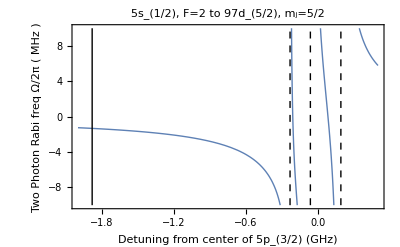

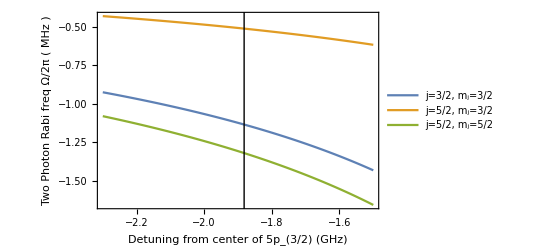

C:\Users\kwnmi\Dropbox\Research\2018\2018-08-14

```mathematica
line1=Line[{{-1.882,-10},{-1.882,10}}];
line2=Line[{{Δhfs[A,3,nucI,jp]/(2π 10^9)/.combinedparamsF2,-10},{Δhfs[A,3,nucI,jp]/(2π 10^9)/.combinedparamsF2,10}}];
line3=Line[{{Δhfs[A,2,nucI,jp]/(2π 10^9)/.combinedparamsF2,-10},{Δhfs[A,2,nucI,jp]/(2π 10^9)/.combinedparamsF2,10}}];
line4=Line[{{Δhfs[A,1,nucI,jp]/(2π 10^9)/.combinedparamsF2,-10},{Δhfs[A,1,nucI,jp]/(2π 10^9)/.combinedparamsF2,10}}];
epilogstyle={{Thick,line1},{Dashed,line2},{Dashed,line3},{Dashed,line4}};

p=Plot[Evaluate[ΩfineRydberg[5/2,5/2]/(2π 10^6)/.f1->f1GHz 10^9],{f1GHz,-2,0.5},Frame->True,FrameLabel->{"Detuning from center of 5p_(3/2) (GHz)","Two Photon Rabi freq \n Ω/2π ( MHz )"},LabelStyle->FontSize->14,PlotStyle->Thick,PlotRange->{-10,10},Epilog->epilogstyle,PlotLabel->"5s_(1/2), F=2 to 97d_(5/2), m_j=5/2"]
Plot[Evaluate[{ΩfineRydberg[3/2,3/2],ΩfineRydberg[5/2,3/2],ΩfineRydberg[5/2,5/2]}/(2π 10^6)/.f1->f1GHz 10^9],{f1GHz,-2.3,-1.5},Frame->True,FrameLabel->{"Detuning from center of 5p_(3/2) (GHz)","Two Photon Rabi freq \n Ω/2π ( MHz )"},PlotRange->Automatic,LabelStyle->FontSize->14,PlotStyle->Thick,Epilog->{Thick,line1},PlotLegends->{"j=3/2, m_j=3/2","j=5/2, m_j=3/2","j=5/2, m_j=5/2"}]
SetDirectory[NotebookDirectory[]]
(*Export["20180329_MK_RydbergRabi.png",p]*)

(*Print[ToString[ΩfineRydberg[5/2,5/2]/(2π 10^6)]<>"MHz Two-photon Rabi frequency to j=5/2, m_j=5/2"]
Table[ΩfineRydberg[j,mj]/(2π 10^6),{j,1/2,5/2},{mj,-j,j}]*)
```

```mathematica
{ΩfineRydberg[3/2,3/2]/(2π 10^6),ΩfineRydberg[5/2,3/2]/(2π 10^6),ΩfineRydberg[5/2,5/2]/(2π 10^6)}/.f1->-1.882 10^9
ΩfineRydberg[5/2,5/2]/(2π 10^6)/.f1->-1.882 10^9
ΩfineRydberg[5/2,5/2]/(2π 10^6)/.f1->-0.882 10^9
```

{-1.13533,-0.51146,-1.32082}

-1.32082

-2.84332

```mathematica
ΩfineRydberg[1/2,1/2]/(2π 10^6)/.f1->-1.882 10^9
```

-0.584739

```mathematica
Single Photon Rabi frequencies
```

```mathematica
Ξgp=ϵ1 e RME1/ℏ;
Ξrp=ϵ2 e RME2/ℏ;
Ξγ1[fp_,fg_,mfg_,q1_]:=Ξgp cj[jp,fp,nucI,jg,fg]ClebschGordan[{fg,mfg},{1,q1},{fp,mfg+q1}];
Ξγ2[fp_,jr_,mjr_,q2_,mfr_,mI_]:=Sum[Ξrp cj[jp,fp,nucI,jr,fr] ClebschGordan[{fr,mfr},{1,-q2},{fp,mfr-q2}]ClebschGordan[{jr,mjr},{nucI,mI},{fr,mfr}]/.combinedparamsF2,{fr,Abs[jr-nucI]/.combinedparamsF2,Abs[jr+nucI]/.combinedparamsF2}]
```

```mathematica
Calculating Differential AC stark shift on 5 Subscript[S, 1/2] F=2 and F=1, from monochromatic light. This is relevant to AAS microwave Ramsey
```

```mathematica
ΔACgF2=Sum[Ξγ1[fp,fg,mg,q1]^2/(4(Δ1-Δhfs[A,fp,nucI,jp])),{fp,0,3}]/.combinedparamsF2;
ΔACgF1=Sum[Ξγ1[fp,fg,mg,q1]^2/(4(Δ2-Δhfs[A,fp,nucI,jp])),{fp,0,3}]/.combinedparamsF1;
Print[ToString[ΔACgF2/(2π 10^6)]<>" MHz on F=2"]
Print[ToString[ΔACgF1/(2π 10^6)]<>" MHz on F=1"]
Print[ToString[(ΔACgF2-ΔACgF1)/(2π 10^6)]<>" MHz between F=2 and F=1"]
```

-2.27603 MHz on F=2

-0.521336 MHz on F=1

-1.75469 MHz between F=2 and F=1

```mathematica
mfr=mg+q1+q2/.combinedparamsF2
mI=mfr-mjr/.combinedparamsF2
```

2

2-mjr

```mathematica
Table[Evaluate[Ξγ1[fp,2,0,1]/(2π 10^6)/.combinedparamsF2],{fp,0,3}]
Table[Evaluate[Ξγ2[fp,5/2,5/2,1,2,-1/2]/(2π 10^6)],{fp,0,3}]
```

{0.,21.1074,81.7486,103.405}

{0.,23.6764,30.5662,19.3317}

## Rabi frequencies in fine structure basis

```mathematica
Ωang[jr_,mjr_,f_,mf_,nucI_,jg_,q1_,q2_,jp_]:=Sum[ClebschGordan[{nucI,mf-mjg},{jg,mjg},{f,mf}]ClebschGordan[{jg,mjg},{1,q1},{jp,mjg+q1}]/Sqrt[2jp+1]ClebschGordan[{jp,mjg+q1},{1,q2},{jr,mjr}]/Sqrt[2jr+1],{mjg,-1/2,1/2}]
```

```mathematica
MatrixForm[Table[{j,mj},{j,1/2,5/2},{mj,-j,j}]]
Print["σ^+, σ^+"]
MatrixForm[Table[Ωang[j,mj,2,0,3/2,1/2,1,1,3/2],{j,1/2,5/2},{mj,-j,j}]]
```

({{1/2,-1/2},{1/2,1/2}}
{{3/2,-3/2},{3/2,-1/2},{3/2,1/2},{3/2,3/2}}
{{5/2,-5/2},{5/2,-3/2},{5/2,-1/2},{5/2,1/2},{5/2,3/2},{5/2,5/2}})

σ^+, σ^+

({0,0}
{0,0,0,-1/(4 √15)}
{0,0,0,0,1/(4 √15),1/(4 √3)})

```mathematica
Print["σ^+, π"]
MatrixForm[Table[Ωang[j,mj,2,0,3/2,1/2,1,0,3/2],{j,1/2,5/2},{mj,-j,j}]]
```

σ^+, π

({0,-1/12}
{0,0,1/(12 √10),(√(3/10))/4}
{0,0,0,1/(4 √15),1/(2 √30),0})